Symmetric Dark Matter

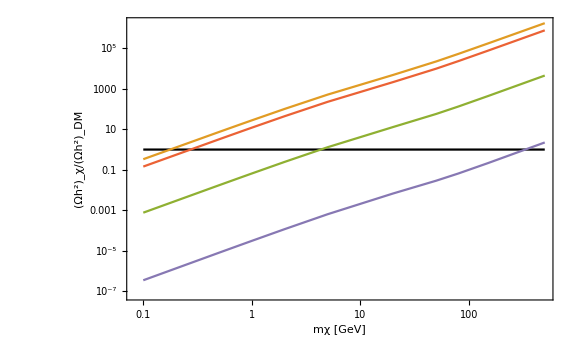

```mathematica
c = 3*^5; (* Speed of light in km/s *)
Mp := 1.22*^19 (* Planck mass in GeV *)
mν := 0;     (*ν  mass *)
me:=0.0005 (*electron mass*)
mμ := 0.105 (*μ mass*)
mτ := 1.800 (*τ mass*)
DensityDM = 0.1129;
GeVtocm2=(1/5.06*^13)^2 ;(* cm^-2*)
GeVtog=(1/1.78*^-24) ;(* g*)
cf=GeVtocm2*GeVtog;
DensityFactor=1.5*^8; (* Product of s0 h^2/Subscript[ρ, c] *)

σvtoZZApprox[g_,m_]:= g^4/(16 Pi m^2)


(* Degree of freedom parameter*)
a:=10.2
b:=2.349
c:=0.252
gs to half [T_]:=a/(1+Exp[-b(T-c)])

(* Functions*)
Yeq[x_]:=0.145 x^1.5 Exp[-x]

DMmassArray ={0.1, 0.5, 0.8,1, 2, 5,20,50, 80,150, 500};
gArray = { 0.008, 0.04, 0.01, 0.3};
RelicArray ={{}, {},{},{}};

ii = 1;
Do[
Do[

BoltzmannP = NDSolve[ {Y'[x] == - Mp (Pi /45)^0.5 gs to half[mass/x] σvtoZZApprox[gprime, mass]  mass (Y[x]^2 - Yeq[x]^2)/x^2, Y[1] == Yeq[1]} , Y, {x, 1, 100},MaxStepFraction->0.0001];YRescaledPrecision[x_] := Evaluate[Y[x] /. BoltzmannP[[1]]];YrescaledPrecission[x_] := YRescaledPrecision[x];RelicDensity = DensityFactor * YrescaledPrecission[100] * mass;
RelicArray[[ii]] =AppendTo[RelicArray[[ii]], RelicDensity/DensityDM],

{mass, DMmassArray} ];
ii++,
{gprime,gArray}]

RelicDensityPlot=ListLinePlot[ {Transpose[{DMmassArray,ConstantArray[1, {Length[DMmassArray]} ] }], 
Transpose[{DMmassArray, RelicArray[[1]]}],
Transpose[{DMmassArray, RelicArray[[2]]}],
Transpose[{DMmassArray, RelicArray[[3]]}],
Transpose[{DMmassArray, RelicArray[[4]]}] }, 
ScalingFunctions->{"Log", "Log"},

BaseStyle->{FontFamily->"Dosis Medium",FontSize->14},
PlotStyle->{Black,MainColor1, BackGroundColor1, Gray1, MainColor2},
Frame->True,
FrameLabel->{"mχ [GeV]", "(Ωh^2)_χ/(Ωh^2)_DM"},
FrameStyle -> Directive[{Black,Thick}],
ImageSize -> Large]
```

```mathematica
DMmassArray ={330,350, 368};

RelicArray ={};

gprime=0.3;
Do[

BoltzmannP = NDSolve[ {Y'[x] == - Mp (Pi /45)^0.5 gs to half[mass/x] σvtoZZApprox[gprime, mass]  mass (Y[x]^2 - Yeq[x]^2)/x^2, Y[1] == Yeq[1]} , Y, {x, 1, 100},MaxStepFraction->0.0001];YRescaledPrecision[x_] := Evaluate[Y[x] /. BoltzmannP[[1]]];YrescaledPrecission[x_] := YRescaledPrecision[x];RelicDensity = DensityFactor * YrescaledPrecission[100] * mass;
RelicArray=AppendTo[RelicArray, RelicDensity/DensityDM],

{mass, DMmassArray} ];
RelicArray
```

{0.995718,1.11675,1.23145}

```mathematica
DMmassArray ={10,11, 12};

RelicArray ={};

gprime=0.06;
Do[

BoltzmannP = NDSolve[ {Y'[x] == - Mp (Pi /45)^0.5 gs to half[mass/x] σvtoZZApprox[gprime, mass]  mass (Y[x]^2 - Yeq[x]^2)/x^2, Y[1] == Yeq[1]} , Y, {x, 1, 100},MaxStepFraction->0.0001];YRescaledPrecision[x_] := Evaluate[Y[x] /. BoltzmannP[[1]]];YrescaledPrecission[x_] := YRescaledPrecision[x];RelicDensity = DensityFactor * YrescaledPrecission[100] * mass;
RelicArray=AppendTo[RelicArray, RelicDensity/DensityDM],

{mass, DMmassArray} ];
RelicArray
```

{0.939656,1.09969,1.26761}

NDSolve::nlnum: The function value {(7.24443×10^8)/(1.+ⅇ^(-2.349 (-0.252+Times[«2»])))} is not a list of numbers with dimensions {1} at {x,Y[x]} = {1.0099,0.0533425}.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

1.60028×10^9

Assymetric Dark Matter

Yield:

```mathematica
mass = 5;
gprime=0.03;

BoltzmannEqs = NDSolve[ {
Yp'[x] == - Mp (Pi /45)^0.5 gs to half[mass/x] σvtoZZApprox[gprime, mass]  mass (Yp[x] Ym[x] - Yeq[x]^2)/x^2, Ym'[x] == - Mp (Pi /45)^0.5 gs to half[mass/x] σvtoZZApprox[gprime, mass]  mass (Yp[x] Ym[x] - Yeq[x]^2)/x^2, 
Yp[1] == 0.8 Yeq[1], 
Ym[1] == Yeq[1] - Yp[1]} , 
{Yp, Ym}, {x, 1, 100},MaxStepFraction->0.0001];
Y[x_] := Evaluate[{Yp[x], Ym[x]}/. BoltzmannEqs[[1]]];
Ychi[x_]:= Y[x][[1]] ;
YchiBar[x_]:= Y[x][[2]] ;

LogLogPlot[{Yeq[x], Ychi[x], YchiBar[x]}, {x,1,100}, PlotRange->{1*^-8, 1}]
```

Relic density:

NDSolve::ndsz: At x == 1., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At x == 1., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

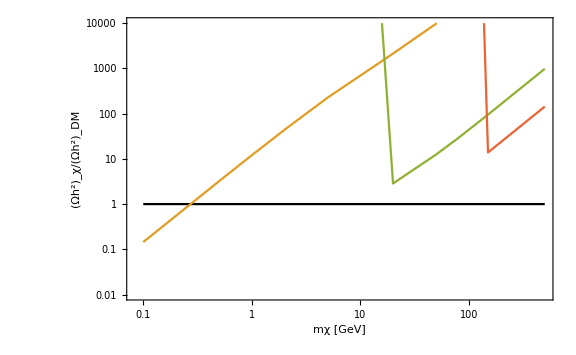

```mathematica
DMmassArray ={0.1, 0.5, 0.8,1, 2, 5,20,50, 80,150, 500};
gArray = {  0.01, 0.06, 0.1, 0.2};
RelicArrayChi ={{}, {},{},{}};
RelicArrayChiBar={{}, {},{},{}};

ii = 1;
Do[
Do[

BoltzmannEqs= NDSolve[ {
Yp'[x] == - Mp (Pi /45)^0.5 gs to half[mass/x] σvtoZZApprox[gprime, mass]  mass (Yp[x] Ym[x] - Yeq[x]^2)/x^2, Ym'[x] == - Mp (Pi /45)^0.5 gs to half[mass/x] σvtoZZApprox[gprime, mass]  mass (Yp[x] Ym[x] - Yeq[x]^2)/x^2, 
Yp[1] == 0.5Yeq[1], 
Ym[1] == Yeq[1] - Yp[1]} , 
{Yp, Ym}, {x, 1, 100},MaxStepFraction->0.0001];
Y[x_] := Evaluate[{Yp[x], Ym[x]}/. BoltzmannEqs[[1]]];
Ychi[x_]:= Y[x][[1]] ;
YchiBar[x_]:= Y[x][[2]] ;

Ochi = DensityFactor *  Ychi[100] * mass;
OchiBar = DensityFactor *  YchiBar[100] * mass;
RelicArrayChi[[ii]] =AppendTo[RelicArrayChi[[ii]], Ochi/DensityDM];
RelicArrayChiBar[[ii]] =AppendTo[RelicArrayChiBar[[ii]], OchiBar/DensityDM],
{mass, DMmassArray} ];
ii++,
{gprime,gArray}]

RelicDensityPlot=ListLinePlot[ {Transpose[{DMmassArray,ConstantArray[1, {Length[DMmassArray]} ] }], 
Transpose[{DMmassArray, RelicArrayChi[[1]]}],
Transpose[{DMmassArray, RelicArrayChi[[2]]}],
Transpose[{DMmassArray, RelicArrayChi[[3]]}],
Transpose[{DMmassArray, RelicArrayChi[[4]]}] }, 
ScalingFunctions->{"Log", "Log"},
PlotRange->{0.01, 1*^4},

BaseStyle->{FontFamily->"Dosis Medium",FontSize->14},
PlotStyle->{Black,MainColor1, BackGroundColor1, Gray1, MainColor2},
Frame->True,
FrameLabel->{"mχ [GeV]", "(Ωh^2)_χ/(Ωh^2)_DM"},
FrameStyle -> Directive[{Black,Thick}],
ImageSize -> Large]
```